# Microcanonical Simulation Project

Benjamin Niehoff
Jose Gonzalez

### General Comments

Our C code generates several data files which we use in this Mathematica notebook to plot some interesting graphs. We will first consider the raw data, that is, temperature, potential energy, total energy, and mean square displacement as functions of time. With these graphs it should be clear when the system reaches equilibrium and if we are close to a phase transition or not.

```mathematica
numberOfParticles = 4*14^3
```

10976

### Raw Output of the Simulation

To convert our dimensionless results to the numbers with proper units we first load the mathematica package that gives us access to several physical constants and another one to convert between units easily.

```mathematica
<<PhysicalConstants`;
<<Units`;
kB=BoltzmannConstant;
NA=AvogadroConstant;
σ=3.405*10^(-10) Meter;
ϵ= 0.996 Kilo Joule/Mole;
τ=2.153*10^(-12) Second;
Subscript[m, Ar]=0.03994 Kilo Gram/Mole;
Atoms=1372;
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

First, let us import the data files and plot them.

```mathematica
SetDirectory[NotebookDirectory[]];
```

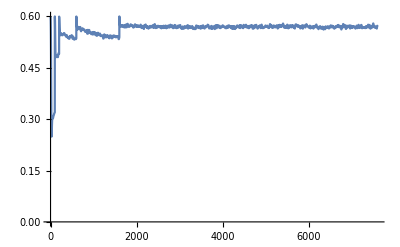

```mathematica
temperature=Import["data_old_format/t0.600_temperature.dat"];
ListLinePlot[temperature, PlotRange -> All]
```

As we can see, after the relaxation time the system reaches equilibrium, which means that the temperature will fluctuate around a constant value. These fluctuations will be used below to calculate the constant-volume specific heat and compare with the slope of the energy vs temperature function.

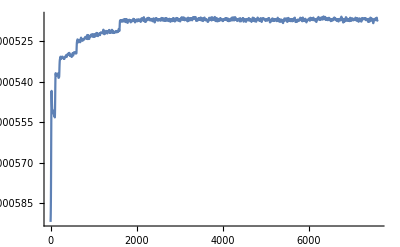

```mathematica
pd=Import["data_old_format/t0.600_potential.dat"];
ListLinePlot[pd, PlotRange->All]
```

As we can see the potential energy also reaches stability.

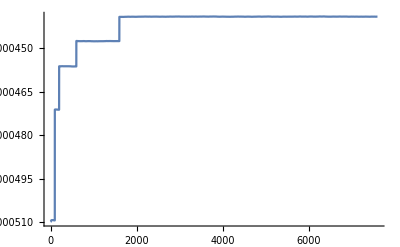

```mathematica
ed = Import["data_old_format/t0.600_total_energy.dat"];
ListLinePlot[ed, PlotRange->All]
```

In this graph we see the total energy also reaches equilibrium. Notice that due to the temperature corrections we make in our algorithm we can see how the system jumps in energy at each correction.

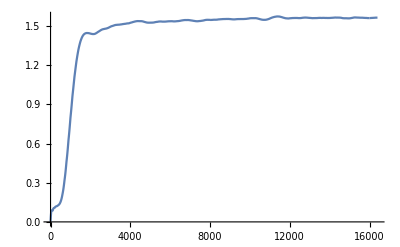

```mathematica
msdd = Import["data_old_format/t0.100_msd.dat"];
ListLinePlot[msdd, PlotRange->All]
```

The mean square displacement gives us a very clear picture of the state the system is in. If the atoms are nearly fixed in their places, the mean square displacement will almost be constant. This corresponds to a solid. When the system is fluid, the graph continually increases:

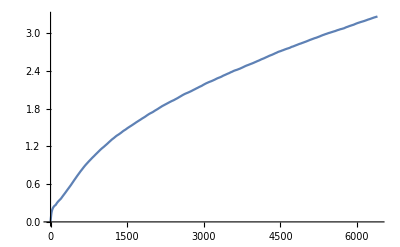

```mathematica
msdd2 = Import["data_old_format/t0.900_msd.dat"];
ListLinePlot[msdd2, PlotRange->All]
```

Here is a histogram of the speeds after equilibrium is reached.  We see that it takes the form of the expected Maxwell distribution.

General::obspkg: Histograms` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

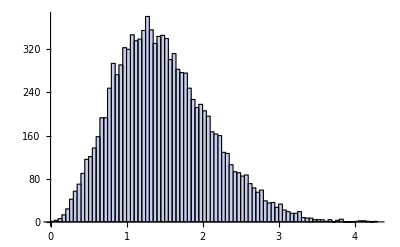

```mathematica
speeds = Import["data_old_format/t0.900_final_speeds.dat", "List"];
Needs["Histograms`"]
Histogram[speeds]
```

Here is the energy vs. temperature.  We see a phase transition around dimensionless temperature 0.45.  This corresponds to

```mathematica
SI[(.45) ϵ / (NA kB)]
```

53.906 Kelvin

The latent heat at the phase transition is approximately

```mathematica
(-5.2-(-6.0)) ϵ
```

(0.7968 Joule Kilo)/Mole

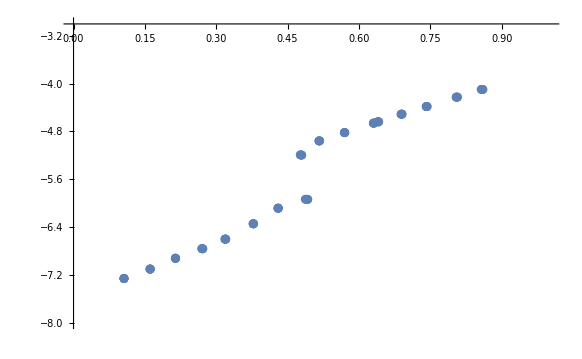

```mathematica
evt = Import["data_old_format/energy_vs_temperature.dat"];
evt = Sort[evt]; 
ListPlot[evt, PlotRange->{{0, 1}, {-8, -3}}]
```

This shows the specific heat.  There is a lot of spread in the data, but the correct value lies within the error bars.  The slope of the E vs T curve is

```mathematica
(-4-(-5))/(1.0 - 0.6)
```

2.5

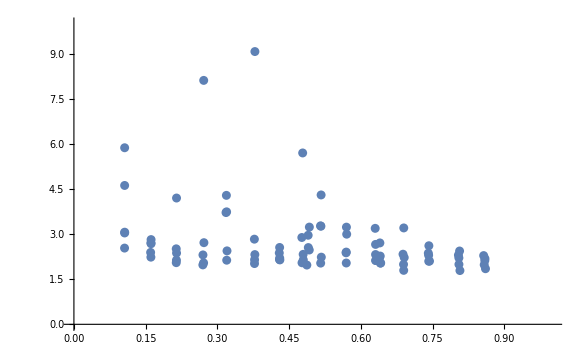

```mathematica
cvvt = Import["data_old_format/cv_vs_temperature.dat"];
cvvt = Sort[cvvt];
ListPlot[cvvt, PlotRange->{{0, 1}, {0, 10}}]
```

The pressure is linear in T for high temperatures as expected.  At low temperatures, there is negative pressure.  This is because the system is held at a fixed volume when it solidifies, and so it is under tension.  Also, in the low temperature region, the pressure begins to increase again toward 0.

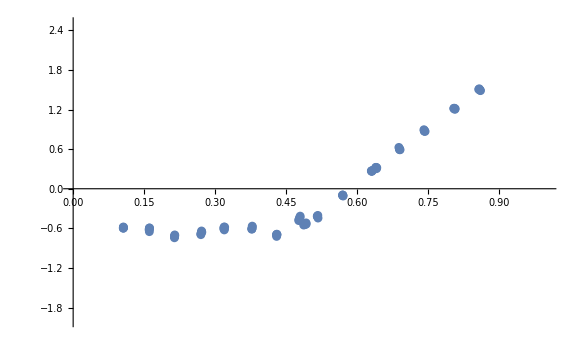

```mathematica
pvt = Import["data_old_format/pressure_vs_temperature.dat"];
pvt = Sort[pvt];
ListPlot[pvt, PlotRange->{{0, 1}, {-2, 2.5}}]
```

Here is an image of the final state of the system at dimensionless temperature 0.1.  We see crystallization, but with a "hole", due to the fact that the crystal lattice occupies less space than is available.  This is the explanation for negative pressure.

```mathematica
Ls = Import["data_old_format/t0.100_box_dimension.dat"];
fp = Import["data_old_format/t0.100_final_positions.dat"];
ListPointPlot3D[fp, BoxRatios->{1,1,1}, ColorFunction->"Rainbow", PlotStyle->PointSize[Small],AxesLabel->{x,y,z}]
```

-Graphics3D-

Here is an example of the final positions at dimensionless temperature 0.9.  Notice how there is no large-scale order, and the atoms fill all the available space:

```mathematica
Ls = Import["data_old_format/t0.900_box_dimension.dat"];
fp = Import["data_old_format/t0.900_final_positions.dat"];
ListPointPlot3D[fp, BoxRatios->{1,1,1}, ColorFunction->"Rainbow", PlotStyle->PointSize[Small],AxesLabel->{x,y,z}]
```

-Graphics3D-